## Phase diagram

### 1.1 Blue points

```mathematica
Clear[betalamdaf];

m=Dimensions[pphasepoints][[1]];
betalamdaf=Table[{0,0,0,0,0,0},{k,1,m}];
k=1;



For[i=1,i<=m,i++,If[pphasepoints[[i,5]]>0,{betalamdaf[[k]]=pphasepoints[[i]];
Print[betalamdaf[[k]]];
k++;}]]

filteredphase=Select[betalamdaf,#[[3]]!=0&];
Dimensions[filteredphase]
```

{0.,0.65102,3.45668,1.51223,1640.28,1244.94}

{0.,0.669388,3.44701,1.47564,8402.31,1345.2}

{0.,0.687755,3.43592,1.44022,18061.6,1454.09}

{0.,0.706122,3.42366,1.406,31610.5,1571.99}

{0.,0.72449,3.41047,1.37299,50326.8,1699.29}

{0.,0.742857,3.39654,1.34117,75841.1,1836.4}

{0.,0.761224,3.38205,1.31053,110215.,1983.71}

{0.,0.779592,3.36714,1.28104,156036.,2141.66}

{0.,0.797959,3.35195,1.25267,216519.,2310.69}

{0.,0.816327,3.33657,1.22538,295633.,2491.27}

{0.,0.834694,3.32111,1.19914,398237.,2683.89}

{0.,0.853061,3.30562,1.17389,530234.,2889.08}

{0.,0.871429,3.29017,1.1496,698740.,3107.36}

{0.,0.889796,3.2748,1.12623,912272.,3339.34}

{0.,0.908163,3.25956,1.10373,1.18094×10^6,3585.62}

{0.,0.926531,3.24447,1.08207,1.51668×10^6,3846.85}

{0.,0.944898,3.22956,1.0612,1.93341×10^6,4123.73}

{0.,0.963265,3.21484,1.04108,2.44733×10^6,4416.98}

{0.,0.981633,3.20032,1.02169,3.07702×10^6,4727.39}

{0.,1.,3.18603,1.00299,3.84371×10^6,5055.79}

{0.0320571,0.65102,3.45849,1.5131,1445.38,1241.58}

{0.0320571,0.669388,3.44886,1.47643,8135.26,1341.68}

{0.0320571,0.687755,3.4378,1.44093,17702.,1450.41}

{0.0320571,0.706122,3.42556,1.40664,31133.5,1568.17}

{0.0320571,0.72449,3.41237,1.37356,49702.3,1695.33}

{0.0320571,0.742857,3.39844,1.34168,75033.1,1832.3}

{0.0320571,0.761224,3.38394,1.31098,109181.,1979.48}

{0.0320571,0.779592,3.36902,1.28144,154726.,2137.3}

{0.0320571,0.797959,3.35381,1.25302,214875.,2306.21}

{0.0320571,0.816327,3.33842,1.22569,293590.,2486.68}

{0.0320571,0.834694,3.32293,1.1994,395718.,2679.19}

{0.0320571,0.853061,3.30742,1.17411,527155.,2884.26}

{0.0320571,0.871429,3.29195,1.14979,695009.,3102.45}

{0.0320571,0.889796,3.27656,1.12638,907787.,3334.33}

{0.0320571,0.908163,3.2613,1.10385,1.1756×10^6,3580.52}

{0.0320571,0.926531,3.24619,1.08216,1.51035×10^6,3841.67}

{0.0320571,0.944898,3.23125,1.06127,1.92599×10^6,4118.47}

{0.0320571,0.963265,3.21651,1.04113,2.43868×10^6,4411.66}

{0.0320571,0.981633,3.20198,1.02172,3.06703×10^6,4722.}

{0.0320571,1.,3.18766,1.00299,3.83227×10^6,5050.35}

{0.0641141,0.65102,3.46392,1.51571,873.733,1231.52}

{0.0641141,0.669388,3.45441,1.4788,7350.27,1331.15}

{0.0641141,0.687755,3.44343,1.44308,16643.1,1439.43}

{0.0641141,0.706122,3.43124,1.40857,29726.6,1556.75}

{0.0641141,0.72449,3.41807,1.37529,47857.9,1683.48}

{0.0641141,0.742857,3.40414,1.34321,72643.8,1820.04}

{0.0641141,0.761224,3.38962,1.31234,106120.,1966.82}

{0.0641141,0.779592,3.37466,1.28263,150844.,2124.26}

{0.0641141,0.797959,3.35941,1.25406,209999.,2292.81}

{0.0641141,0.816327,3.34396,1.22659,287522.,2472.92}

{0.0641141,0.834694,3.32842,1.20017,388234.,2665.1}

{0.0641141,0.853061,3.31284,1.17477,518002.,2869.86}

{0.0641141,0.871429,3.29731,1.15034,683908.,3087.74}

{0.0641141,0.889796,3.28185,1.12683,894434.,3319.34}

{0.0641141,0.908163,3.26652,1.10422,1.15966×10^6,3565.26}

{0.0641141,0.926531,3.25134,1.08244,1.49149×10^6,3826.16}

{0.0641141,0.944898,3.23634,1.06147,1.90384×10^6,4102.73}

{0.0641141,0.963265,3.22153,1.04126,2.41288×10^6,4395.71}

{0.0641141,0.981633,3.20694,1.02178,3.03723×10^6,4705.87}

{0.0641141,1.,3.19256,1.003,3.79813×10^6,5034.04}

{0.0961712,0.669388,3.46366,1.48279,6094.66,1313.75}

{0.0961712,0.687755,3.45283,1.44669,14943.1,1421.27}

{0.0961712,0.706122,3.44072,1.41181,27460.7,1537.84}

{0.0961712,0.72449,3.4276,1.37819,44878.8,1663.86}

{0.0961712,0.742857,3.41366,1.3458,68775.,1799.72}

{0.0961712,0.761224,3.39911,1.31463,101152.,1945.84}

{0.0961712,0.779592,3.3841,1.28465,144531.,2102.64}

{0.0961712,0.797959,3.36877,1.25582,202056.,2270.57}

{0.0961712,0.816327,3.35323,1.22811,277619.,2450.1}

{0.0961712,0.834694,3.33759,1.20148,376000.,2641.71}

{0.0961712,0.853061,3.32191,1.17588,503019.,2845.94}

{0.0961712,0.871429,3.30626,1.15127,665712.,3063.32}

{0.0961712,0.889796,3.2907,1.1276,872518.,3294.44}

{0.0961712,0.908163,3.27526,1.10482,1.13348×10^6,3539.92}

{0.0961712,0.926531,3.25997,1.08291,1.46047×10^6,3800.4}

{0.0961712,0.944898,3.24485,1.06181,1.86738×10^6,4076.59}

{0.0961712,0.963265,3.22994,1.04148,2.37038×10^6,4369.21}

{0.0961712,0.981633,3.21524,1.0219,2.98808×10^6,4679.05}

{0.0961712,1.,3.20075,1.00301,3.74178×10^6,5006.95}

{0.128228,0.669388,3.47661,1.48846,4443.44,1289.66}

{0.128228,0.687755,3.466,1.4518,12694.5,1396.1}

{0.128228,0.706122,3.45403,1.41642,24448.8,1511.62}

{0.128228,0.72449,3.44097,1.3823,40901.9,1636.62}

{0.128228,0.742857,3.42704,1.34946,63590.5,1771.51}

{0.128228,0.761224,3.41245,1.31787,94471.7,1916.69}

{0.128228,0.779592,3.39737,1.28749,136015.,2072.58}

{0.128228,0.797959,3.38193,1.25831,191310.,2239.65}

{0.128228,0.816327,3.36628,1.23027,264188.,2418.35}

{0.128228,0.834694,3.3505,1.20333,359368.,2609.18}

{0.128228,0.853061,3.33467,1.17745,482604.,2812.65}

{0.128228,0.871429,3.31887,1.15258,640869.,3029.33}

{0.128228,0.889796,3.30315,1.12867,842542.,3259.78}

{0.128228,0.908163,3.28755,1.10568,1.09761×10^6,3504.63}

{0.128228,0.926531,3.2721,1.08357,1.41789×10^6,3764.53}

{0.128228,0.944898,3.25683,1.06229,1.81727×10^6,4040.17}

{0.128228,0.963265,3.24177,1.0418,2.31187×10^6,4332.3}

{0.128228,0.981633,3.22691,1.02206,2.92035×10^6,4641.7}

{0.128228,1.,3.21229,1.00304,3.66402×10^6,4969.21}

{0.160285,0.669388,3.49324,1.49587,2493.83,1259.18}

{0.160285,0.687755,3.48295,1.4585,10018.2,1364.21}

{0.160285,0.706122,3.47119,1.42244,20839.3,1478.36}

{0.160285,0.72449,3.45824,1.38769,36107.4,1602.04}

{0.160285,0.742857,3.44433,1.35425,57307.3,1735.65}

{0.160285,0.761224,3.4297,1.3221,86337.2,1879.6}

{0.160285,0.779592,3.41453,1.29122,125601.,2034.33}

{0.160285,0.797959,3.39898,1.26156,178118.,2200.27}

{0.160285,0.816327,3.38316,1.23308,247643.,2377.89}

{0.160285,0.834694,3.36721,1.20575,338811.,2567.69}

{0.160285,0.853061,3.3512,1.1795,457297.,2770.2}

{0.160285,0.871429,3.3352,1.15429,609988.,2985.95}

{0.160285,0.889796,3.31927,1.13007,805184.,3215.54}

{0.160285,0.908163,3.30347,1.1068,1.0528×10^6,3459.57}

{0.160285,0.926531,3.28782,1.08443,1.3646×10^6,3718.72}

{0.160285,0.944898,3.27235,1.06291,1.7544×10^6,3993.66}

{0.160285,0.963265,3.25708,1.0422,2.23834×10^6,4285.16}

{0.160285,0.981633,3.24203,1.02227,2.83507×10^6,4593.99}

{0.160285,1.,3.22721,1.00306,3.56598×10^6,4921.}

{0.192342,0.669388,3.51351,1.50513,358.049,1222.68}

{0.192342,0.687755,3.50368,1.46687,7054.75,1325.94}

{0.192342,0.706122,3.49222,1.42996,16806.6,1438.4}

{0.192342,0.72449,3.47943,1.39441,30709.,1560.43}

{0.192342,0.742857,3.46559,1.36023,50184.1,1692.46}

{0.192342,0.761224,3.45094,1.32739,77058.8,1834.89}

{0.192342,0.779592,3.43567,1.29586,113658.,1988.15}

{0.192342,0.797959,3.41997,1.26561,162913.,2152.7}

{0.192342,0.816327,3.40398,1.23659,228485.,2328.99}

{0.192342,0.834694,3.38781,1.20875,314910.,2517.53}

{0.192342,0.853061,3.37157,1.18204,427759.,2718.83}

{0.192342,0.871429,3.35533,1.15641,573818.,2933.44}

{0.192342,0.889796,3.33915,1.13181,761286.,3161.96}

{0.192342,0.908163,3.3231,1.10819,999987.,3405.}

{0.192342,0.926531,3.30719,1.08549,1.3016×10^6,3663.21}

{0.192342,0.944898,3.29147,1.06368,1.67991×10^6,3937.3}

{0.192342,0.963265,3.27596,1.04271,2.15101×10^6,4228.02}

{0.192342,0.981633,3.26067,1.02253,2.73357×10^6,4536.15}

{0.192342,1.,3.24561,1.0031,3.44905×10^6,4862.55}

{0.224399,0.687755,3.52816,1.47703,3955.41,1281.75}

{0.224399,0.706122,3.51714,1.43909,12540.,1392.14}

{0.224399,0.72449,3.50461,1.40257,24941.,1512.19}

{0.224399,0.742857,3.49089,1.36748,42507.2,1642.31}

{0.224399,0.761224,3.47623,1.3338,66982.7,1782.91}

{0.224399,0.779592,3.46088,1.30149,100599.,1934.42}

{0.224399,0.797959,3.44503,1.27052,146184.,2097.28}

{0.224399,0.816327,3.42883,1.24083,207289.,2271.98}

{0.224399,0.834694,3.41241,1.21238,288330.,2458.99}

{0.224399,0.853061,3.3959,1.18512,394756.,2658.86}

{0.224399,0.871429,3.37937,1.15898,533229.,2872.11}

{0.224399,0.889796,3.3629,1.13391,711826.,3099.35}

{0.224399,0.908163,3.34654,1.10986,940264.,3341.19}

{0.224399,0.926531,3.33033,1.08678,1.23013×10^6,3598.3}

{0.224399,0.944898,3.31431,1.06461,1.59512×10^6,3871.37}

{0.224399,0.963265,3.2985,1.04331,2.05132×10^6,4161.16}

{0.224399,0.981633,3.28292,1.02284,2.6174×10^6,4468.47}

{0.224399,1.,3.26758,1.00314,3.31489×10^6,4794.14}

{0.256457,0.687755,3.55635,1.48912,871.427,1232.14}

{0.256457,0.706122,3.54594,1.44995,8231.92,1340.1}

{0.256457,0.72449,3.5338,1.41228,19044.6,1457.81}

{0.256457,0.742857,3.52028,1.3761,34575.7,1585.67}

{0.256457,0.761224,3.50568,1.34141,56474.3,1724.1}

{0.256457,0.779592,3.49027,1.30817,86865.2,1873.54}

{0.256457,0.797959,3.47425,1.27634,128458.,2034.43}

{0.256457,0.816327,3.45783,1.24586,184675.,2207.24}

{0.256457,0.834694,3.44115,1.21669,259796.,2392.47}

{0.256457,0.853061,3.42432,1.18876,359125.,2590.64}

{0.256457,0.871429,3.40747,1.16201,489178.,2802.31}

{0.256457,0.889796,3.39065,1.13639,657893.,3028.05}

{0.256457,0.908163,3.37393,1.11184,874851.,3268.5}

{0.256457,0.926531,3.35737,1.08829,1.15153×10^6,3524.31}

{0.256457,0.944898,3.34099,1.06571,1.50153×10^6,3796.2}

{0.256457,0.963265,3.32483,1.04403,1.9409×10^6,4084.92}

{0.256457,0.981633,3.30891,1.0232,2.48832×10^6,4391.26}

{0.256457,1.,3.29323,1.00319,3.16538×10^6,4716.09}

{0.288514,0.706122,3.57858,1.4627,4066.06,1282.86}

{0.288514,0.72449,3.56702,1.42367,13254.7,1397.83}

{0.288514,0.742857,3.55383,1.38622,26684.6,1523.06}

{0.288514,0.761224,3.53937,1.35034,45899.4,1658.97}

{0.288514,0.779592,3.52394,1.31599,72904.4,1806.}

{0.288514,0.797959,3.50779,1.28315,110276.,1964.6}

{0.288514,0.816327,3.49113,1.25174,161289.,2135.23}

{0.288514,0.834694,3.47415,1.22171,230068.,2318.4}

{0.288514,0.853061,3.45699,1.193,321752.,2514.62}

{0.288514,0.871429,3.43976,1.16555,442689.,2724.44}

{0.288514,0.889796,3.42254,1.13928,600651.,2948.46}

{0.288514,0.908163,3.40542,1.11413,805064.,3187.31}

{0.288514,0.926531,3.38844,1.09005,1.06726×10^6,3441.64}

{0.288514,0.944898,3.37166,1.06698,1.40077×10^6,3712.17}

{0.288514,0.963265,3.35509,1.04486,1.82153×10^6,3999.66}

{0.288514,0.981633,3.33877,1.02363,2.34826×10^6,4304.91}

{0.288514,1.,3.32271,1.00325,3.00262×10^6,4628.8}

{0.320571,0.706122,3.61497,1.47752,205.666,1221.1}

{0.320571,0.72449,3.60425,1.43691,7785.42,1332.91}

{0.320571,0.742857,3.59159,1.39797,19109.7,1455.11}

{0.320571,0.761224,3.57739,1.3607,35606.9,1588.11}

{0.320571,0.779592,3.56202,1.32507,59150.4,1732.37}

{0.320571,0.797959,3.54577,1.29104,92168.7,1888.33}

{0.320571,0.816327,3.5289,1.25855,137774.,2056.46}

{0.320571,0.834694,3.51161,1.22752,199913.,2237.26}

{0.320571,0.853061,3.49407,1.19791,283540.,2431.25}

{0.320571,0.871429,3.47642,1.16962,394811.,2638.97}

{0.320571,0.889796,3.45876,1.14261,541308.,2861.03}

{0.320571,0.908163,3.44118,1.11678,732276.,3098.05}

{0.320571,0.926531,3.42374,1.09208,978893.,3350.71}

{0.320571,0.944898,3.40648,1.06844,1.29454×10^6,3619.7}

{0.320571,0.963265,3.38945,1.04581,1.69511×10^6,3905.8}

{0.320571,0.981633,3.37267,1.02412,2.19929×10^6,4209.83}

{0.320571,1.,3.35617,1.00331,2.82882×10^6,4532.65}

{0.352628,0.72449,3.64542,1.45218,2818.41,1263.78}

{0.352628,0.742857,3.63355,1.41153,12092.4,1382.5}

{0.352628,0.761224,3.61981,1.37265,25910.3,1512.19}

{0.352628,0.779592,3.60463,1.33553,46002.9,1653.27}

{0.352628,0.797959,3.58835,1.30013,74636.6,1806.22}

{0.352628,0.816327,3.57129,1.26637,114744.,1971.5}

{0.352628,0.834694,3.5537,1.2342,170076.,2149.61}

{0.352628,0.853061,3.53577,1.20353,245378.,2341.06}

{0.352628,0.871429,3.51767,1.1743,346592.,2546.42}

{0.352628,0.889796,3.49952,1.14641,481081.,2766.26}

{0.352628,0.908163,3.48142,1.1198,657885.,3001.23}

{0.352628,0.926531,3.46345,1.09439,887994.,3251.99}

{0.352628,0.944898,3.44567,1.07011,1.18464×10^6,3519.26}

{0.352628,0.963265,3.42811,1.04689,1.56362×10^6,3803.82}

{0.352628,0.981633,3.41081,1.02467,2.04358×10^6,4106.48}

{0.352628,1.,3.3938,1.00339,2.64635×10^6,4428.12}

{0.384685,0.742857,3.67965,1.42709,5827.62,1306.04}

{0.384685,0.761224,3.66666,1.38636,17073.7,1431.94}

{0.384685,0.779592,3.65185,1.34753,33809.2,1569.42}

{0.384685,0.797959,3.63568,1.31054,58126.3,1718.95}

{0.384685,0.816327,3.61851,1.27533,92761.8,1881.}

{0.384685,0.834694,3.60063,1.24183,141252.,2056.06}

{0.384685,0.853061,3.58231,1.20996,208111.,2244.65}

{0.384685,0.871429,3.56373,1.17962,299041.,2447.33}

{0.384685,0.889796,3.54504,1.15075,421160.,2664.69}

{0.384685,0.908163,3.52638,1.12324,583272.,2897.36}

{0.384685,0.926531,3.50782,1.09701,796151.,3146.01}

{0.384685,0.944898,3.48944,1.072,1.07285×10^6,3411.36}

{0.384685,0.963265,3.47129,1.04811,1.42904×10^6,3694.2}

{0.384685,0.981633,3.4534,1.02529,1.88333×10^6,3995.35}

{0.384685,1.,3.43581,1.00347,2.45761×10^6,4315.7}

{0.416742,0.742857,3.72973,1.44488,454.469,1226.6}

{0.416742,0.761224,3.71789,1.40204,9298.39,1348.2}

{0.416742,0.779592,3.70376,1.36123,22849.,1481.6}

{0.416742,0.797959,3.68789,1.32242,43012.7,1627.26}

{0.416742,0.816327,3.67072,1.28554,72315.9,1785.65}

{0.416742,0.834694,3.65263,1.25052,114061.,1957.28}

{0.416742,0.853061,3.63392,1.21726,172511.,2142.66}

{0.416742,0.871429,3.61485,1.18567,253098.,2342.34}

{0.416742,0.889796,3.5956,1.15566,362671.,2556.91}

{0.416742,0.908163,3.57631,1.12712,509765.,2787.01}

{0.416742,0.926531,3.5571,1.09998,704905.,3033.31}

{0.416742,0.944898,3.53805,1.07413,960935.,3296.54}

{0.416742,0.963265,3.51924,1.04949,1.29337×10^6,3577.48}

{0.416742,0.981633,3.50069,1.026,1.72076×10^6,3876.97}

{0.416742,1.,3.48246,1.00357,2.26505×10^6,4195.9}

{0.448799,0.761224,3.77336,1.41992,2715.75,1261.92}

{0.448799,0.779592,3.76034,1.37686,13323.1,1390.69}

{0.448799,0.797959,3.74506,1.33596,29584.1,1531.98}

{0.448799,0.816327,3.72809,1.29716,53801.6,1686.25}

{0.448799,0.834694,3.7099,1.26039,89027.3,1854.01}

{0.448799,0.853061,3.69087,1.22555,139249.,2035.78}

{0.448799,0.871429,3.67131,1.19252,209606.,2232.1}

{0.448799,0.889796,3.65147,1.16121,306646.,2443.57}

{0.448799,0.908163,3.63151,1.13151,438601.,2670.81}

{0.448799,0.926531,3.61159,1.10332,615715.,2914.51}

{0.448799,0.944898,3.59181,1.07652,850586.,3175.39}

{0.448799,0.963265,3.57226,1.05104,1.15854×10^6,3454.24}

{0.448799,0.981633,3.55297,1.02679,1.55805×10^6,3751.91}

{0.448799,1.,3.53401,1.00367,2.07108×10^6,4069.31}

{0.480856,0.779592,3.82146,1.39464,5346.16,1297.68}

{0.480856,0.797959,3.80723,1.35136,18031.5,1434.02}

{0.480856,0.816327,3.79077,1.31037,37507.,1583.65}

{0.480856,0.834694,3.77267,1.2716,66557.6,1747.07}

{0.480856,0.853061,3.75342,1.23494,108875.,1924.78}

{0.480856,0.871429,3.73342,1.20027,169281.,2117.35}

{0.480856,0.889796,3.71297,1.16749,253988.,2325.35}

{0.480856,0.908163,3.69232,1.13646,370894.,2549.42}

{0.480856,0.926531,3.67163,1.10707,529922.,2790.23}

{0.480856,0.944898,3.65105,1.07922,743385.,3048.52}

{0.480856,0.963265,3.63067,1.05278,1.02639×10^6,3325.08}

{0.480856,0.981633,3.61057,1.02767,1.39728×10^6,3620.77}

{0.480856,1.,3.5908,1.00379,1.87803×10^6,3936.5}

{0.512913,0.797959,3.8743,1.36886,8444.38,1334.41}

{0.512913,0.816327,3.85881,1.32537,23604.8,1478.8}

{0.512913,0.834694,3.84111,1.28431,46931.9,1637.32}

{0.512913,0.853061,3.82183,1.24557,81802.4,1810.49}

{0.512913,0.871429,3.80148,1.20903,132694.,1998.85}

{0.512913,0.889796,3.78047,1.17456,205453.,2202.99}

{0.512913,0.908163,3.75909,1.14203,307607.,2423.53}

{0.512913,0.926531,3.73759,1.1113,448716.,2661.16}

{0.512913,0.944898,3.71614,1.08224,640768.,2916.59}

{0.512913,0.963265,3.69486,1.05473,898609.,3190.64}

{0.512913,0.981633,3.67385,1.02866,1.24041×10^6,3484.16}

{0.512913,1.,3.65317,1.00392,1.68814×10^6,3798.09}

{0.54497,0.797959,3.94597,1.38871,812.149,1234.26}

{0.54497,0.816327,3.93216,1.34239,12149.8,1372.74}

{0.54497,0.834694,3.91534,1.29872,30295.2,1525.75}

{0.54497,0.853061,3.89634,1.25761,58292.7,1693.81}

{0.54497,0.871429,3.87582,1.21894,100251.,1877.46}

{0.54497,0.889796,3.85432,1.18255,161622.,2077.29}

{0.54497,0.908163,3.83224,1.1483,249522.,2293.91}

{0.54497,0.926531,3.80989,1.11604,373107.,2527.99}

{0.54497,0.944898,3.7875,1.08562,543992.,2780.29}

{0.54497,0.963265,3.76524,1.0569,776713.,3051.58}

{0.54497,0.981633,3.74323,1.02976,1.08924×10^6,3342.74}

{0.54497,1.,3.72155,1.00407,1.50348×10^6,3654.71}

{0.577027,0.816327,4.01057,1.36169,3083.88,1266.62}

{0.577027,0.834694,3.99536,1.31507,16658.8,1413.42}

{0.577027,0.853061,3.97712,1.27126,38455.2,1575.73}

{0.577027,0.871429,3.95673,1.23014,72191.5,1754.09}

{0.577027,0.889796,3.93491,1.19157,122893.,1949.08}

{0.577027,0.908163,3.91219,1.15537,197228.,2161.33}

{0.577027,0.926531,3.88899,1.12137,303903.,2391.5}

{0.577027,0.944898,3.86562,1.08942,454108.,2640.32}

{0.577027,0.963265,3.8423,1.05934,662019.,2908.58}

{0.577027,0.981633,3.81919,1.03099,945344.,3197.17}

{0.577027,1.,3.7964,1.00423,1.32591×10^6,3507.04}

{0.609084,0.834694,4.08096,1.33359,5908.2,1301.49}

{0.609084,0.853061,4.06424,1.28672,22249.2,1457.3}

{0.609084,0.871429,4.04447,1.24282,48579.8,1629.72}

{0.609084,0.889796,4.0226,1.20175,89470.4,1819.3}

{0.609084,0.908163,3.99939,1.16333,151104.,2026.66}

{0.609084,0.926531,3.97538,1.12737,241689.,2252.46}

{0.609084,0.944898,3.951,1.09367,371938.,2497.44}

{0.609084,0.963265,3.92655,1.06206,555608.,2762.37}

{0.609084,0.981633,3.90225,1.03236,810096.,3048.16}

{0.609084,1.,3.87824,1.00442,1.15709×10^6,3355.74}

{0.641141,0.853061,4.15755,1.30423,9495.8,1339.73}

{0.641141,0.871429,4.13917,1.25718,29316.6,1505.42}

{0.641141,0.889796,4.11775,1.21327,61371.4,1688.9}

{0.641141,0.908163,4.0943,1.17232,111320.,1890.79}

{0.641141,0.926531,4.06961,1.13412,186826.,2111.72}

{0.641141,0.944898,4.04423,1.09846,298066.,2352.42}

{0.641141,0.963265,4.01861,1.06511,458316.,2613.69}

{0.641141,0.981633,3.99302,1.0339,684597.,2896.4}

{0.641141,1.,3.96768,1.00462,998396.,3201.51}

{0.673198,0.871429,4.2408,1.27344,14152.1,1382.37}

{0.673198,0.889796,4.22059,1.22631,38431.7,1558.97}

{0.673198,0.908163,4.19737,1.18248,77838.1,1754.68}

{0.673198,0.926531,4.17222,1.14174,139443.,1970.16}

{0.673198,0.944898,4.14595,1.10383,232827.,2206.1}

{0.673198,0.963265,4.11913,1.06854,370715.,2463.3}

{0.673198,0.981633,4.09218,1.03561,569683.,2742.62}

{0.673198,1.,4.06539,1.00485,850958.,3045.05}

{0.705255,0.871429,4.34901,1.29185,2709.05,1261.85}

{0.705255,0.889796,4.33121,1.24106,20325.5,1430.65}

{0.705255,0.908163,4.30897,1.19396,50428.1,1619.39}

{0.705255,0.926531,4.2838,1.15033,99448.1,1828.71}

{0.705255,0.944898,4.25681,1.10989,176311.,2059.33}

{0.705255,0.963265,4.22885,1.07238,293115.,2311.99}

{0.705255,0.981633,4.20049,1.03754,465916.,2587.58}

{0.705255,1.,4.17216,1.00511,715602.,2887.06}

{0.737313,0.889796,4.44939,1.25776,6592.19,1305.2}

{0.737313,0.908163,4.42933,1.20696,28686.1,1486.02}

{0.737313,0.926531,4.40485,1.16004,66544.7,1688.39}

{0.737313,0.944898,4.37754,1.11672,128374.,1912.99}

{0.737313,0.963265,4.34858,1.0767,225571.,2160.59}

{0.737313,0.981633,4.31882,1.03969,373580.,2432.02}

{0.737313,1.,4.28884,1.00539,592871.,2728.27}

{0.76937,0.908163,4.55843,1.22166,12065.8,1355.82}

{0.76937,0.926531,4.5358,1.17102,40252.6,1550.27}

{0.76937,0.944898,4.50883,1.12442,88656.,1768.06}

{0.76937,0.963265,4.4792,1.08157,167889.,2009.94}

{0.76937,0.981633,4.44812,1.04211,292692.,2276.73}

{0.76937,1.,4.41645,1.00572,483019.,2569.4}

{0.801427,0.926531,4.67687,1.18343,19941.3,1415.52}

{0.801427,0.944898,4.65133,1.13313,56605.9,1625.55}

{0.801427,0.963265,4.6216,1.08706,119654.,1860.94}

{0.801427,0.981633,4.58945,1.04484,223017.,2122.5}

{0.801427,1.,4.55611,1.00608,386029.,2411.17}

{0.833484,0.926531,4.82788,1.19745,4867.52,1285.41}

{0.833484,0.944898,4.80555,1.14298,31515.8,1486.55}

{0.833484,0.963265,4.77672,1.09326,80252.4,1714.52}

{0.833484,0.981633,4.74397,1.04791,164093.,1970.14}

{0.833484,1.,4.7091,1.00649,301627.,2254.31}

{0.865541,0.944898,4.9717,1.15408,12559.2,1352.23}

{0.865541,0.963265,4.94542,1.10026,48911.2,1571.69}

{0.865541,0.981633,4.91292,1.05137,115258.,1820.5}

{0.865541,1.,4.87686,1.00696,229309.,2099.56}

{0.897598,0.963265,5.12839,1.10815,24732.6,1433.49}

{0.897598,0.981633,5.09758,1.05528,75686.3,1674.44}

{0.897598,1.,5.06101,1.00749,168376.,1947.64}

{0.929655,0.963265,5.32596,1.11702,6738.89,1301.07}

{0.929655,0.981633,5.29922,1.05968,44427.8,1532.9}

{0.929655,1.,5.26331,1.0081,117965.,1799.29}

{0.961712,0.981633,5.51895,1.06464,20448.2,1396.84}

{0.961712,1.,5.48572,1.00879,77091.6,1655.26}

{0.993769,0.981633,5.75749,1.07018,2672.66,1267.27}

{0.993769,1.,5.73024,1.00959,44687.7,1516.3}

{1.02583,1.,5.99889,1.0105,19644.9,1383.16}

{1.05788,1.,6.29342,1.01155,853.61,1256.64}

{388,6}

### 1.2 start and square points

```mathematica
lamdafbetag10low[[All,{1,2}]]
lamdafbetag10high[[All,{1,2}]]
```

{{0.1,0.392877},{0.114833,0.394994},{0.129667,0.397393},{0.1445,0.400068},{0.159333,0.403017},{0.174167,0.406233},{0.189,0.409712},{0.203833,0.413449},{0.218667,0.417439},{0.2335,0.421675},{0.248333,0.426153},{0.263167,0.430866},{0.278,0.435809},{0.292833,0.440977},{0.307667,0.446363},{0.3225,0.451962},{0.337333,0.45777},{0.352167,0.46378},{0.367,0.469988},{0.381833,0.476388},{0.396667,0.482976},{0.4115,0.489747},{0.426333,0.496698},{0.43,0.498443},{0.441167,0.503823},{0.456,0.511119},{0.470833,0.518583},{0.485667,0.52621},{0.5005,0.533998},{0.515333,0.541945},{0.530167,0.550046},{0.545,0.558301},{0.559833,0.566706},{0.574667,0.575261},{0.5895,0.583964},{0.604333,0.592814},{0.619167,0.601811},{0.634,0.610953},{0.648833,0.620242},{0.663667,0.629679},{0.6785,0.639265},{0.693333,0.649002},{0.708167,0.658894},{0.723,0.668946},{0.737833,0.679162},{0.752667,0.689551},{0.7675,0.700123},{0.782333,0.710892},{0.797167,0.721874},{0.812,0.733095},{0.826833,0.744585},{0.841667,0.75639},{0.8565,0.768571},{0.871333,0.781222},{0.886167,0.794479},{0.901,0.808562},{0.915833,0.823834},{0.930667,0.840951},{0.9455,0.861223},{0.960333,0.887695},{0.97,0.911973},{0.975167,0.929476},{0.98,0.950964},{0.99,1.03284},{0.992,1.06364},{0.994,1.10601},{0.996,1.16872},{0.998,1.27236},{1,1.57079}}

{{0.1,0.705255},{0.118367,0.673198},{0.136735,0.705255},{0.155102,0.737313},{0.173469,0.737313},{0.191837,0.737313},{0.210204,0.737313},{0.228571,0.737313},{0.246939,0.737313},{0.265306,0.737313},{0.283673,0.737313},{0.302041,0.76937},{0.320408,0.76937},{0.338776,0.76937},{0.357143,0.76937},{0.37551,0.76937},{0.393878,0.801427},{0.412245,0.801427},{0.430612,0.801427},{0.44898,0.801427},{0.467347,0.833484},{0.485714,0.833484},{0.504082,0.833484},{0.522449,0.833484},{0.540816,0.865541},{0.559184,0.865541},{0.577551,0.865541},{0.595918,0.897598},{0.614286,0.897598},{0.632653,0.897598},{0.65102,0.929655},{0.669388,0.929655},{0.687755,0.929655},{0.706122,0.961712},{0.72449,0.961712},{0.742857,0.993769},{0.761224,0.993769},{0.779592,1.02583},{0.797959,1.02583},{0.816327,1.05788},{0.834694,1.05788},{0.853061,1.08994},{0.871429,1.08994},{0.889796,1.122},{0.908163,1.15405},{0.926531,1.15405},{0.944898,1.18611},{0.963265,1.21817},{0.981633,1.25023},{1.,1.5708}}

```mathematica
(*betalow={{0.3928767261768801,0.1},{0.3949941404371214,0.11483333333333333},{0.39739274056682067,0.12966666666666668},{0.40006844526535756,0.14450000000000002},{0.4030168268290032,0.15933333333333333},{0.40623315422038514,0.17416666666666666},{0.40971243710133465,0.189},{0.413449470076843,0.20383333333333334},{0.417438876463396,0.21866666666666668},{0.42167515097492714,0.23349999999999999},{0.4261527008091268,0.24833333333333332},{0.43086588471143045,0.26316666666666666},{0.43580904968944184,0.278},{0.44097656514351147,0.29283333333333333},{0.44636285426683997,0.30766666666666664},{0.4519624226489092,0.3225},{0.45776988408800723,0.3373333333333334},{0.46377998368152884,0.35216666666666663},{0.4699876183166654,0.367},{0.4763878547295486,0.38183333333333336},{0.48297594533884863,0.3966666666666666},{0.4897473420914995,0.4115},{0.49669770858520157,0.42633333333333334},{0.49844288438716833,0.43},{0.5038229307563857,0.4411666666666666},{0.5111191264454111,0.456},{0.5185826541752969,0.4708333333333334},{0.5262101215085494,0.4856666666666667},{0.5339983933821055,0.5005000000000001},{0.5419446008663408,0.5153333333333333},{0.5500461508553302,0.5301666666666667},{0.5583007372778815,0.545},{0.566706354530083,0.5598333333333333},{0.5752613139806785,0.5746666666666667},{0.5839642646048864,0.5895},{0.5928142190804141,0.6043333333333333},{0.6018105870597292,0.6191666666666666},{0.610953217856057,0.634},{0.6202424555064081,0.6488333333333334},{0.629679210190994,0.6636666666666666},{0.6392650514261425,0.6785},{0.6490023305074356,0.6933333333333332},{0.6588943426713046,0.7081666666666666},{0.6689455438556453,0.723},{0.679161843560076,0.7378333333333333},{0.6895510054287413,0.7526666666666666},{0.7001232029845147,0.7675},{0.7108918032090222,0.7823333333333332},{0.7218744921202359,0.7971666666666666},{0.7330949265564862,0.812},{0.7445852187720797,0.8268333333333333},{0.7563897825724955,0.8416666666666668},{0.7685714908726916,0.8565},{0.7812219349376026,0.8713333333333333},{0.7944793568544035,0.8861666666666667},{0.8085618871186178,0.901},{0.8238338402434999,0.9158333333333333},{0.84095107530528,0.9306666666666668},{0.8612230092379988,0.9455},{0.8876947835129901,0.9603333333333333},{0.9119731976641392,0.97},{0.929475553611149,0.9751666666666666},{0.9509640334820129,0.98},{1.0328405622544128,0.99},{1.0636444222204715,0.992},{1.10601284295065,0.994},{1.1687211697637854,0.996},{1.2723618680585365,0.998},{1.5707934420230742,1}};

betahigh={{0.7052554936630148,0.1},{0.6731984257692414,0.11836734693877551},{0.7052554936630148,0.13673469387755102},{0.7373125615567883,0.15510204081632656},{0.7373125615567883,0.17346938775510204},{0.7373125615567883,0.19183673469387755},{0.7373125615567883,0.21020408163265306},{0.7373125615567883,0.2285714285714286},{0.7373125615567883,0.24693877551020407},{0.7373125615567883,0.26530612244897955},{0.7373125615567883,0.28367346938775506},{0.7693696294505615,0.30204081632653057},{0.7693696294505615,0.32040816326530613},{0.7693696294505615,0.3387755102040816},{0.7693696294505615,0.35714285714285715},{0.7693696294505615,0.3755102040816326},{0.801426697344335,0.39387755102040817},{0.801426697344335,0.4122448979591837},{0.801426697344335,0.43061224489795913},{0.801426697344335,0.4489795918367347},{0.8334837652381084,0.46734693877551015},{0.8334837652381084,0.4857142857142857},{0.8334837652381084,0.5040816326530612},{0.8334837652381084,0.5224489795918367},{0.8655408331318817,0.5408163265306123},{0.8655408331318817,0.5591836734693878},{0.8655408331318817,0.5775510204081632},{0.8975979010256552,0.5959183673469387},{0.8975979010256552,0.6142857142857142},{0.8975979010256552,0.6326530612244898},{0.9296549689194286,0.6510204081632652},{0.9296549689194286,0.6693877551020407},{0.9296549689194286,0.6877551020408162},{0.9617120368132019,0.7061224489795919},{0.9617120368132019,0.7244897959183674},{0.9937691047069754,0.7428571428571428},{0.9937691047069754,0.7612244897959183},{1.0258261726007487,0.7795918367346938},{1.0258261726007487,0.7979591836734694},{1.0578832404945222,0.8163265306122448},{1.0578832404945222,0.8346938775510203},{1.0899403083882955,0.8530612244897958},{1.0899403083882955,0.8714285714285714},{1.121997376282069,0.889795918367347},{1.1540544441758425,0.9081632653061223},{1.1540544441758425,0.9265306122448979},{1.1861115120696157,0.9448979591836734},{1.2181685799633892,0.963265306122449},{1.2502256478571625,0.9816326530612245},{1.5707963267948966,1.}};
```

### 1.3 Phase diagram plots

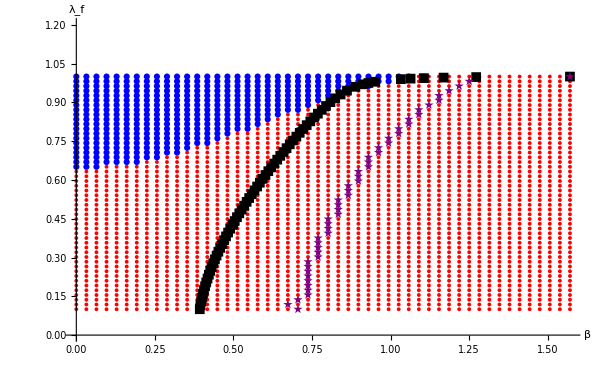

```mathematica
G1=ListPlot[filteredphase[[All,{1,2}]],PlotStyle->Blue];
G2=ListPlot[Flatten[Table[{beta,lamdaf},{beta,0,Pi/2,Pi/(2*49)},{lamdaf,0.1,1,0.9/49}],1],PlotStyle->Red,AxesLabel->{"β","λ_f"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black],PlotRange->{0,1.2}];
G3=ListPlot[betalow,PlotMarkers->{"■",10},PlotStyle->{Black}];
G4=ListPlot[betahigh,PlotMarkers->{"★",10},PlotStyle->{Purple}];


Show[G2,G1,G3,G4]
```

```mathematica
SuperStar[β] (Subscript[ϕ, f]=0.5)
```

```mathematica
betalow={{0.1,0.3928767261768801},{0.11483333333333333,0.3949941404371214},{0.12966666666666668,0.39739274056682067},{0.14450000000000002,0.40006844526535756},{0.15933333333333333,0.4030168268290032},{0.17416666666666666,0.40623315422038514},{0.189,0.40971243710133465},{0.20383333333333334,0.413449470076843},{0.21866666666666668,0.417438876463396},{0.23349999999999999,0.42167515097492714},{0.24833333333333332,0.4261527008091268},{0.26316666666666666,0.43086588471143045},{0.278,0.43580904968944184},{0.29283333333333333,0.44097656514351147},{0.30766666666666664,0.44636285426683997},{0.3225,0.4519624226489092},{0.3373333333333334,0.45776988408800723},{0.35216666666666663,0.46377998368152884},{0.367,0.4699876183166654},{0.38183333333333336,0.4763878547295486},{0.3966666666666666,0.48297594533884863},{0.4115,0.4897473420914995},{0.42633333333333334,0.49669770858520157},{0.43,0.49844288438716833},{0.4411666666666666,0.5038229307563857},{0.456,0.5111191264454111},{0.4708333333333334,0.5185826541752969},{0.4856666666666667,0.5262101215085494},{0.5005000000000001,0.5339983933821055},{0.5153333333333333,0.5419446008663408},{0.5301666666666667,0.5500461508553302},{0.545,0.5583007372778815},{0.5598333333333333,0.566706354530083},{0.5746666666666667,0.5752613139806785},{0.5895,0.5839642646048864},{0.6043333333333333,0.5928142190804141},{0.6191666666666666,0.6018105870597292},{0.634,0.610953217856057},{0.6488333333333334,0.6202424555064081},{0.6636666666666666,0.629679210190994},{0.6785,0.6392650514261425},{0.6933333333333332,0.6490023305074356},{0.7081666666666666,0.6588943426713046},{0.723,0.6689455438556453},{0.7378333333333333,0.679161843560076},{0.7526666666666666,0.6895510054287413},{0.7675,0.7001232029845147},{0.7823333333333332,0.7108918032090222},{0.7971666666666666,0.7218744921202359},{0.812,0.7330949265564862},{0.8268333333333333,0.7445852187720797},{0.8416666666666668,0.7563897825724955},{0.8565,0.7685714908726916},{0.8713333333333333,0.7812219349376026},{0.8861666666666667,0.7944793568544035},{0.901,0.8085618871186178},{0.9158333333333333,0.8238338402434999},{0.9306666666666668,0.84095107530528},{0.9455,0.8612230092379988},{0.9603333333333333,0.8876947835129901},{0.97,0.9119731976641392},{0.9751666666666666,0.929475553611149},{0.98,0.9509640334820129},{0.99,1.0328405622544128},{0.992,1.0636444222204715},{0.994,1.10601284295065},{0.996,1.1687211697637854},{0.998,1.2723618680585365},{1,1.5707934420230742}};

betahigh={{0.1,0.7052554936630148},{0.11836734693877551,0.6731984257692414},{0.13673469387755102,0.7052554936630148},{0.15510204081632656,0.7373125615567883},{0.17346938775510204,0.7373125615567883},{0.19183673469387755,0.7373125615567883},{0.21020408163265306,0.7373125615567883},{0.2285714285714286,0.7373125615567883},{0.24693877551020407,0.7373125615567883},{0.26530612244897955,0.7373125615567883},{0.28367346938775506,0.7373125615567883},{0.30204081632653057,0.7693696294505615},{0.32040816326530613,0.7693696294505615},{0.3387755102040816,0.7693696294505615},{0.35714285714285715,0.7693696294505615},{0.3755102040816326,0.7693696294505615},{0.39387755102040817,0.801426697344335},{0.4122448979591837,0.801426697344335},{0.43061224489795913,0.801426697344335},{0.4489795918367347,0.801426697344335},{0.46734693877551015,0.8334837652381084},{0.4857142857142857,0.8334837652381084},{0.5040816326530612,0.8334837652381084},{0.5224489795918367,0.8334837652381084},{0.5408163265306123,0.8655408331318817},{0.5591836734693878,0.8655408331318817},{0.5775510204081632,0.8655408331318817},{0.5959183673469387,0.8975979010256552},{0.6142857142857142,0.8975979010256552},{0.6326530612244898,0.8975979010256552},{0.6510204081632652,0.9296549689194286},{0.6693877551020407,0.9296549689194286},{0.6877551020408162,0.9296549689194286},{0.7061224489795919,0.9617120368132019},{0.7244897959183674,0.9617120368132019},{0.7428571428571428,0.9937691047069754},{0.7612244897959183,0.9937691047069754},{0.7795918367346938,1.0258261726007487},{0.7979591836734694,1.0258261726007487},{0.8163265306122448,1.0578832404945222},{0.8346938775510203,1.0578832404945222},{0.8530612244897958,1.0899403083882955},{0.8714285714285714,1.0899403083882955},{0.889795918367347,1.121997376282069},{0.9081632653061223,1.1540544441758425},{0.9265306122448979,1.1540544441758425},{0.9448979591836734,1.1861115120696157},{0.963265306122449,1.2181685799633892},{0.9816326530612245,1.2502256478571625},{1.,1.5707963267948966}};
```

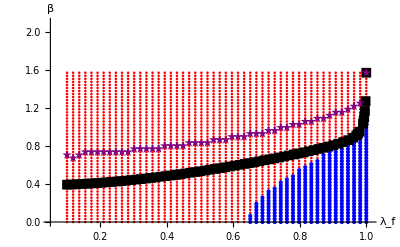

```mathematica
G1=ListPlot[filteredphase[[All,{2,1}]],PlotStyle->Blue];
G2=ListPlot[Flatten[Table[{lamdaf,beta},{lamdaf,0.1,1,0.9/49},{beta,0,Pi/2,Pi/(2*49)}],1],PlotStyle->Red,AxesLabel->{"λ_f","β"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black],PlotRange->{{0.05,1.01},{0,2.1}}];
G3=ListPlot[betalow,PlotMarkers->{"■",10},PlotStyle->{Black}];
G4=ListPlot[betahigh,PlotMarkers->{"★",10},PlotStyle->{Purple}];


Show[G2,G1,G3,G4]
```